## Generating Coupled Exponential Random Variables

### Coupled Box-Müller Method

The coupled Box-Muller algorithm than has the following procedure.

1)	Draw two uniform random variables U1 and U2 over the range 0 to 1.
2)	Apply the generalized transformation  (Z_1,Z_2)=T(U_1,U_2) where T is
	 	Z_1=√(ln_κ(U_1^-2))cos(2π U_2)
Z_2=√(ln_κ(U_2^-2))sin(2π U_1).	
In this case the dimension of the logarithm is zero and thus the variable U does not need to be raised to a power.
3)	(Z_1,Z_2)  forms a two-dimensional coupled Gaussian  distribution with  μ_1=μ_2=0 and Σ^(−1)=(1 | 0
0 | 1). For a set of independent random variables only one of the two variates should be selected, since although uncorrelated (no cross terms in the correlation matrix) the variates are dependent since the joint distribution cannot be factored. 
4)	The location and scale for the coupled Gaussian variates are added to Z by  X=μ+σZ.

```mathematica
Clear[CoupledVariate];
CoupledVariate[μ_:0,σ_:1,κ_,n_:1] :=Module[
{UniformVariates=RandomReal[{0,1},2n],CoupledNormalVariates},
CoupledNormalVariates =
If[n==1,
√CoupledLogarithm[UniformVariates⟦1⟧^-2,κ,0] Cos[2π UniformVariates⟦-1⟧],
Table[
√CoupledLogarithm[UniformVariates⟦i⟧^-2,κ,0] Cos[2π UniformVariates⟦-i⟧],
{i,n}
]
];
μ+σ CoupledNormalVariates
];
```

The following recursive approach is slower, probably because two uniform variates have to be generated each time, so it will not be used.

```mathematica
CoupledVariateRecursion[μ_:0,σ_:1,κ_,n_:1] :=Module[
{UniformVariates=RandomReal[{0,1},2],CoupledNormalVariates},
CoupledNormalVariates =
If[n≥1,
Join[
{√CoupledLogarithm[UniformVariates⟦1⟧^-2,κ,0] Cos[2π UniformVariates⟦-1⟧]},
CoupledVariateRecursion[μ,σ,κ,n-1]
],
{}
];
μ+σ CoupledNormalVariates
];
```

#### Test Speed of Coupled Variate Generation

```mathematica
Timing[CoupledVariate[0,1,0.5,100]]
```

{0.001402,{1.44734,-0.699994,0.100969,-2.33016,1.61307,0.621156,0.352804,-3.13991,1.36538,-0.82268,0.541339,-0.0685702,0.318485,0.625484,0.541354,0.589265,0.0226059,2.07785,1.49498,-2.04162,-0.327448,1.4749,1.57659,0.512373,-1.48103,2.88186,-0.712832,-1.16296,0.936102,-0.607952,0.613602,0.505231,-2.8156,1.78993,-3.93682,2.47669,-1.70283,-0.763286,-0.0911208,-0.107362,3.20009,0.313251,0.44376,0.5707,-1.91018,-0.64095,0.612857,-0.816989,0.333209,0.618438,-6.18593,0.715747,-10.9072,-3.54173,0.77551,0.988723,0.136242,-1.07115,1.62387,1.56286,0.116278,1.78457,0.0937525,0.226239,-1.52575,0.193962,-1.99443,1.19347,-0.65169,-0.221486,-0.300489,-7.45428,1.01693,2.33273,-0.743679,0.0863837,2.85944,0.0231974,-1.69603,0.394012,-0.940115,3.46488,-1.37612,1.23092,-1.53462,-0.746134,-0.0508108,0.725828,-0.0233953,0.362475,0.00751013,0.691596,-9.33157,1.48568,0.255052,-0.643062,-4.39021,-5.07094,1.10197,0.0941189}}

```mathematica
Timing[CoupledVariateRecursion[0,1,0.5,100]]
```

{0.002787,{0.793072,-2.86334,-0.497931,0.656407,1.12343,1.13591,-1.47265,15.3612,1.48796,1.94676,0.648156,-0.842023,-1.57257,-0.0647861,-0.717372,1.79062,1.12537,0.522964,0.32825,1.86567,0.215172,1.62458,-2.10747,0.493554,1.13914,1.38107,5.05458,0.311467,0.730632,-0.0426198,0.0135975,0.464987,-0.558422,-1.17774,-1.11799,-0.951534,-2.08255,-1.83885,-0.824215,-0.17043,-0.437774,-0.403622,0.772632,1.12621,0.663818,-1.94469,-0.185478,0.514791,0.362546,-1.06064,-0.220772,1.05727,-0.649148,1.47165,-1.09506,-0.132802,-0.765618,1.32928,-1.64227,1.17851,2.18116,0.226294,2.82013,1.18989,0.193469,-0.159083,5.01688,-0.540012,4.34838,-1.01169,0.750724,-2.41829,0.288725,0.432759,-0.651514,0.661682,-0.553925,-0.855164,-0.75085,-1.67477,-0.409563,0.810416,1.0057,-0.130611,0.513724,0.110543,0.697425,-0.997091,5.3269,0.278365,0.71126,-1.56775,-2.06519,-1.32206,1.00946,-0.412239,-0.757344,-2.13607,-1.37186,1.67274}}

### Multivariate Coupled Box-Müller Method

The method is based on polar version of the Box-Muller method. The advantage is there is a clear procedure for extending the method to multiple dimensions. The disadvantage is that method uses sample rejection to form a unit n-sphere. Since the n-sphere is based on R^2=x_1^2+... x_n^2as n increases the number of rejected samples increases.  This will make the algorithm very slow for large dimensions.

```mathematica
Clear[CoupledVariate];
CoupledVariate::lsigma="Length of scale `1` does not equal length of mean `2`";
CoupledVariate[μ_:0,Σ_:1,κ_:1,n_:1] :=Module[
{UniformVariates,CoupledNormalVariates,radiusSquared,
dimMean,dimScale,σAdj,j},
dimMean=Length[μ];
σAdj=If[(dimScale=Length[Σ])≠dimMean,
Message[CoupledVariate::lsigma,dimScale,dimMean];
(*If[dimScale>dimMean,
Σ⟦;;dimMean⟧,
PadRight[Σ,dimMean-dimScale,1],
Σ
]*)
];
UniformVariates=Table[0,n,Max[2,dimMean]];
radiusSquared=Table[0,n];
For[j=1,j≤n,j++,
While[Not[0<radiusSquared⟦j⟧<1],
UniformVariates⟦j⟧=RandomReal[{-1,1},Max[2,dimMean]];
(* Dividing by √Max[2,dimMean] seems to make solution closer to a multivarirate t distribution, but needs to be proven; also this factor shouldn't change radiusSquared from being a uniform distribution, but it will reduce the number of rejections; furthermore this should be the same a drawing from a domain reduced from from {-1,1} *)

radiusSquared⟦j⟧=(*1/(√Max[2,dimMean])*)∑_(i=1)^Max[2,dimMean] UniformVariates⟦j,i⟧^2;
]
];

If[n==1,
CoupledNormalVariates=Table[√(CoupledLogarithm[radiusSquared⟦1⟧^-2,κ,0]/radiusSquared⟦1⟧) UniformVariates⟦1,i⟧,
{i,dimMean}
];
μ+CoupledNormalVariates.CholeskyDecomposition[Σ],
Table[
CoupledNormalVariates=Table[√(CoupledLogarithm[radiusSquared⟦j⟧^-2,κ,0]/radiusSquared⟦j⟧) UniformVariates⟦j,i⟧,
{i,dimMean}
];
μ+CoupledNormalVariates.CholeskyDecomposition[Σ],
{j,n}
]

]
];
```

#### Examples compared with Mathematica MultivariateT generation

```mathematica
ListPointPlot3D[CoupledVariate[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}},1,10000],
PlotTheme->"Detailed",
AxesLabel->{"x","y","z"},
PlotRange->Table[{-25,25},3]
]
```

-Graphics3D-

```mathematica
ListPointPlot3D[RandomVariate[MultivariateTDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}},1],10000],
PlotTheme->"Detailed",
AxesLabel->{"x","y","z"},
PlotRange->Table[{-25,25},3]
]
```

-Graphics3D-

Examples side by side of CoupledVariate (left or top) and MultivariateT (right or bottom) variates show reasonable similarity

[{mean},{correlation matrix}, coupling, samples]
[{-2,1,1},{{4,1,0},{1,2,1},{0,1,1}},3,10000]

```mathematica
-Graphics3D--Graphics3D-
```

[{-2,1,1},{{4,1,0},{1,2,1},{0,1,1}},5,10000]

```mathematica
-Graphics3D--Graphics3D-
```

Cauchy Standard

```mathematica
-Graphics3D--Graphics3D-
```

#### Speed comparison for 20-dimensional case

Generate a random 20x20 positive definite metric and test that Cholesky Decomposition is valid

```mathematica
randomMean = RandomReal[{-1,1},#]&/@{5,10,15,20};
randomMatrix = RandomReal[{0,1},{#,#}]&/@{5,10,15,20};
randomCorrelation =ConjugateTranspose[#].#&/@randomMatrix;
(*CholeskyDecomposition[randomCorrelation];*)
```

```mathematica
Dimensions[randomMatrix[[2]]]
```

{10,10}

Speed Test of dimensions 5, 10,  15, and 20

```mathematica
Table[RepeatedTiming[Mean[CoupledVariate[randomMean⟦i⟧,randomCorrelation⟦i⟧,1,1]]],{i,4}]
```

{{0.00012,1.61127},{0.005,0.000170068},{0.4,0.545694},{900.,0.375721}}

```mathematica
900/360
```

5/2

2 1/2 hours

```mathematica
Table[RepeatedTiming[Mean[RandomVariate[MultivariateTDistribution[randomMean⟦i⟧,randomCorrelation⟦i⟧,1],1]]],{i,4}]
```

{{0.00018,{-4.4427,-2.01438,-1.53474,-3.18718,-3.89616}},{0.0002,{3.57148,2.80651,3.37953,3.82085,4.36319,1.36897,1.48233,1.37016,4.0599,3.57476}},{0.0002,{-3.90685,-1.37639,-1.51145,0.370022,-3.25075,-2.54838,-0.0978394,-2.55664,-1.98115,-1.80041,-2.21647,-1.75433,-5.19025,-4.02266,-1.13834}},{0.0002,{7.79328,1.95635,1.83012,1.25876,2.87197,1.05773,1.5922,0.0536025,0.552745,0.953732,2.03771,5.89976,-1.9536,-0.496707,5.27366,1.22267,2.94615,-0.772169,0.506554,-2.28069}}}

Speed Test of dimensions 5, 10, and 15

```mathematica
Table[RepeatedTiming[Mean[CoupledVariate[randomMean⟦i⟧,randomCorrelation⟦i⟧,1,1]]],{i,3}]
```

{{0.0001,0.243764},{0.005,0.150609},{0.78,0.0335082}}

```mathematica
Table[RepeatedTiming[Mean[RandomVariate[MultivariateTDistribution[randomMean⟦i⟧,randomCorrelation⟦i⟧,1],1]]],{i,3}]
```

{{0.00018,{-3.76504,-16.2006,-478.904,-345.679,-239.08}},{0.00019,{2.18052,3.15168,1.82034,0.969079,0.74849,1.68407,3.34733,1.21577,2.23545,-0.349965}},{0.000201,{-1.43072,-0.227768,0.605498,-2.08254,0.120507,-2.75789,-0.146772,-1.47632,2.4422,-0.471717,0.219661,-0.911263,-1.64883,-1.85933,-2.54888}}}

Verify CoupledVariate Output:  May want to consider making the dimension 1 case a 1-d vector so its output is like the MultivariateTDistribution

```mathematica
CoupledVariate[randomMean⟦1⟧,randomCorrelation⟦1⟧,1,1]
```

{-0.11888,0.841234,0.716779,0.398186,0.766867}

```mathematica
RandomVariate[MultivariateTDistribution[randomMean⟦1⟧,randomCorrelation⟦1⟧,1],1]
```

{{3.40181,3.16069,2.5428,3.20363,4.98041}}

### Plots with √κ multiplied by 1/σ

#### Function to Produce Plot

```mathematica
PlotCoupledDistSamples[dist_,estPDF_,samples_,μ_,σ_,κ_]:=Module[
{h,ArrowDetails,f,g},
h=Graphics[Line[{{0,3/4},{0,-3/4}}]];
ArrowDetails={
(*Text["Scale",{μ+σ/2,f-0.03}],
Text["Fluctuations", {μ+σ+√Abs[κ]/(1.1σ),g+0.02}],*)
Text[Style["μ",12],{μ,f+0.04}],
Text[Style["σ",12],{μ+σ+.25,f+0.04}],
Text[Style["1/σ",12],{μ+1/σ-0.,g+If[κ≥0,0.05,-0.05]}],
Text[Style[If[κ<0,"- ",""]<>"(√(2 | κ |))/σ",8],{μ+1/σ+Sign[κ]√(2Abs[κ])/σ +If[κ≥0,-0.7,1.25],
g+If[κ≥0,0.1,0.1]}],
PointSize[Medium],
Point[{μ,f}],Point[{μ+1/σ,g}],Point[{μ-1/σ,g}],
(* Standard Deviation *)
Arrowheads[{{0.02,1,{h,0}}}],
Arrow[{{μ,f},{μ+σ,f}}],
Arrow[{{μ,f},{μ-σ,f}}],
(* Fluctuation *)
Arrowheads[{(*{0.02,0,{h,0}},*).03}],
Arrow[{{μ+1/σ(*-Sign[κ]√((2Abs[κ])/(1+κ))/σ*),g},{μ+1/σ+ Sign[κ]√(2Abs[κ])/σ,g}}],
Arrow[{{μ-1/σ(*+Sign[κ]√((2Abs[κ])/(1+κ))/σ*),g},{μ-1/σ-Sign[κ]√(2Abs[κ])/σ,g}}]
}/.{f->PDF[dist,μ+σ],g->PDF[dist,μ+1/σ]};

Show[
Plot[
{PDF[dist,x],
Style[estPDF,Dashed]
},
{x,-5,5},
PlotTheme->{"Detailed"},
PlotRange->{{-5,5},{-0.1,0.9}},
PlotLegends->Placed[{
Style["Theoretical Density",Smaller],
Style["Emperical Density",Smaller]},
{{.27,.85},Center}],
PlotRange->Full,
PlotLabel->Style["Coupled Gaussian μ="<>ToString[μ]<>", σ="<>ToString[σ]<>", κ="<>ToString[κ],Medium],
FrameLabel->{Style["x",Medium],Style["Density",Medium]},
Epilog->ArrowDetails
],
ListPlot[
Transpose@{samples⟦1;;5000⟧,RandomReal[{-0.1,-0.01},
Length[samples⟦1;;5000⟧]]}
]
]
]
```

Test Function

```mathematica
μ=0;σ=1;κ=1;
dist=CoupledNormalDistribution[μ,σ,κ];
CoupledVariates=CoupledVariate[μ,σ,κ,100000];
```

```mathematica
estPDF=PDF[SmoothKernelDistribution[CoupledVariates,{"Adaptive",Automatic,0.25}],x];
```

```mathematica
estPDF=PDF[EstimatedDistribution[CoupledVariates,CauchyDistribution[α,β]],x];
```

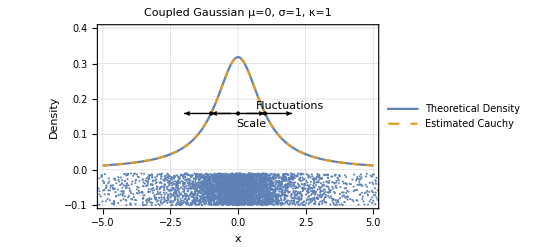

```mathematica
PlotCoupledDistSamples[dist,estPDF,CoupledVariates,μ,σ,κ]
```

Saved Image

-Graphics-

```mathematica
μ=1;σ=0.5;κ=0.5;
dist=CoupledNormalDistribution[μ,σ,κ];
CoupledVariates=CoupledVariate[μ,σ,κ,100000];
estPDF=PDF[SmoothKernelDistribution[CoupledVariates,{"Adaptive",0.75,0.5}],x];
```

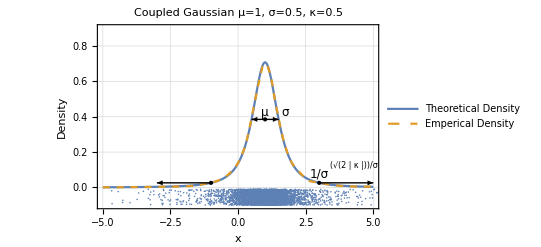

```mathematica
PlotCoupledDistSamples[dist,estPDF,CoupledVariates,μ,σ,κ]
```

```mathematica
μ=1;σ=0.5;κ=-0.333;
dist=CoupledNormalDistribution[μ,σ,κ];
CoupledVariates=CoupledVariate[μ,σ,κ,100000];
estPDF=PDF[SmoothKernelDistribution[CoupledVariates,(*"Silverman"*){"Adaptive",0.75,0.5},(*{"Bounded",{μ-σ/√Abs[κ],μ-σ/√Abs[κ]},*)"SemiCircle"(*}*)],x];
```

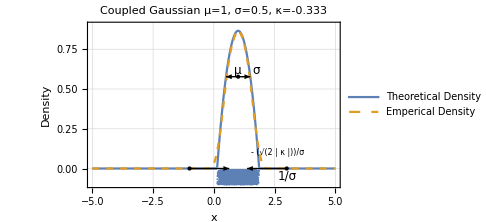

```mathematica
PlotCoupledDistSamples[dist,estPDF,CoupledVariates,μ,σ,κ]
```

#### Coupled Gaussian with κ = 0.5 and σ = 1/2

```mathematica
μ=1;σ=1/2;κ=0.5;
```

```mathematica
CoupledVariates=CoupledVariate[μ,σ,κ,10000];
```

```mathematica
EstimatedDensity=PDF[SmoothKernelDistribution[CoupledVariates,{"Adaptive",0.75,0.3}],x];
```

```mathematica
h=Graphics[Line[{{0,1/2},{0,-1/2}}]];
ArrowDetails={
Text["μ",{μ,f+0.03}],
Text["σ",{μ+σ-.1,f+0.03}],
Text["1/σ",{μ+1/σ+0.1,f+g+0.05}],
Text["√κ/σ",{μ+1/σ+√κ/σ+.2,f+g+0.025}],
PointSize[Medium],
Point[{μ,f}],Point[{μ+1/σ,f+g}],Point[{μ-1/σ,f+g}],
(* Standard Deviation *)
Arrowheads[{{Medium,0,{h,0}},{Medium,1,{h,0}}}],
Arrow[{{μ-σ,f},{μ+σ,f}}],
(*Arrow[{{μ,f},{μ+σ,f}}],
Arrow[{{μ,f},{μ-σ,f}}],*)
(* Fluctuation *)
Arrowheads[{-.02,.02}],

Arrow[{{μ+1/σ-√(κ/(1+κ))/σ,f+g},{μ+1/σ+ √κ/σ,f+g}}],
Arrow[{{μ-1/σ+√(κ/(1+κ))/σ,f+g},{μ-1/σ-√κ/σ,f+g}}]
}/.{f->0,g->PDF[CoupledNormalDistribution[μ,σ,κ],μ+1/σ]};
Show[
Plot[
{PDF[CoupledNormalDistribution[μ,σ,κ],x],
Style[EstimatedDensity,Dashed]
},
{x,-10,10},
PlotTheme->"Detailed",
PlotRange->{{-10,10},{-0.05,0.75}},
PlotLegends->Placed[{
Style["Theoretical Density",Smaller],
Style["Empirical Density",Smaller]},
{{.27,.85},Center}],
PlotRange->Full,
(*PlotLabel->Style["Coupled Gaussian μ=1, σ=0.5, κ=0.5",Large],*)
(*FrameLabel->{Style["x"Large],Style["Density"Large]},*)
Epilog->ArrowDetails
],
ListPlot[
Transpose@{CoupledVariates,RandomReal[{-0.05,-0.01},10000]}(*,
Directive[LightBlue]*)
]
]
```

Transpose::nmtx: The first two levels of {{0.910558,0.864147,0.157931,-5.19587,0.473371,0.788602,«39»,0.953352,0.694285,0.809928,1.72069,1.70801,«99950»},{«1»}} cannot be transposed.

ListPlot::lpn: Transpose[{{0.910558,0.864147,0.157931,-5.19587,0.473371,0.788602,«40»,0.694285,0.809928,1.72069,1.70801,«99950»},{«1»}}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[Transpose[{{0.910558,0.864147,0.157931,-5.19587,0.473371,«41»,0.694285,0.809928,1.72069,1.70801,«99950»},{«1»}}]]].

#### Coupled Gaussian with κ = 0.5 and σ = 2

```mathematica
μ=1;σ=2;κ=0.5;
```

```mathematica
CoupledVariates=CoupledVariate[μ,σ,κ,10000];
```

```mathematica
EstimatedDensity=PDF[SmoothKernelDistribution[CoupledVariates,{"Adaptive",0.75,0.3}],x];
```

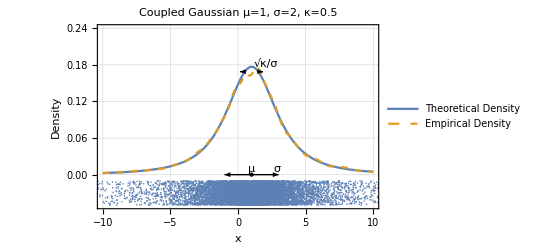

```mathematica
h=Graphics[Line[{{0,1/2},{0,-1/2}}]];
ArrowDetails={
Text["μ",{μ,f+0.01}],
Text["σ",{μ+σ-.1,f+0.01}],
Text["√κ/σ",{μ+1/σ+√κ/σ+.2,f+g+0.013}],
PointSize[Medium],
Point[{μ,f}],
(* Standard Deviation *)
Arrowheads[{{Medium,1,{h,0}}}],
Arrow[{{μ,f},{μ+σ,f}}],
Arrow[{{μ,f},{μ-σ,f}}],
(* Fluctuation *)
Arrowheads[Small],
Arrow[{{μ+1/σ,f+g},{μ+1/σ+ √κ/σ,f+g}}],
Arrow[{{μ-1/σ,f+g},{μ-1/σ-√κ/σ,f+g}}]}/.
{f->0,g->PDF[CoupledNormalDistribution[μ,σ,κ],μ+1/σ]};
Show[
Plot[
{PDF[CoupledNormalDistribution[μ,σ,κ],x],
Style[EstimatedDensity,Dashed]
},
{x,-10,10},
PlotTheme->"Detailed",
PlotRange->{{-10,10},{-0.05,0.24}},
PlotLegends->Placed[{
Style["Theoretical Density",Smaller],
Style["Empirical Density",Smaller]},
{{.27,.85},Center}],
PlotRange->Full,
PlotLabel->"Coupled Gaussian μ=1, σ=2, κ=0.5",
FrameLabel->{"x","Density"},
Epilog->ArrowDetails
],
ListPlot[
Transpose@{CoupledVariates,RandomReal[{-0.05,-0.01},10000]}(*,
Directive[LightBlue]*)
]
]
```

### Backup of Originals Generate and Plot Examples

Cauchy Example, κ = 1

```mathematica
CauchyVariates=CoupledVariate[0,1,1,1000];
CauchyWolframVariates=RandomVariate[CauchyDistribution[],1000];
```

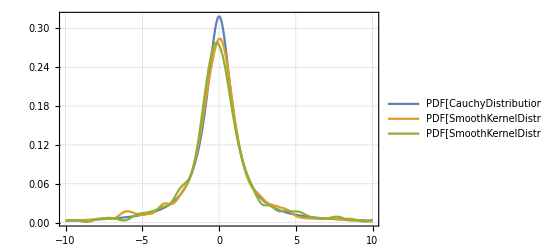

```mathematica
Plot[
{PDF[CauchyDistribution[0,1],x],
PDF[SmoothKernelDistribution[CauchyVariates],x],
PDF[SmoothKernelDistribution[CauchyWolframVariates],x]
},
{x,-10,10},
PlotTheme->"Detailed",
PlotRange->Full
]
(*Histogram[CauchyVariates,"Wand","PDF",
PlotRange->Full]*)
```

Cauchy Example, κ = 1

```mathematica
CauchyVariates=CoupledVariate[0,1,1,10000];
```

```mathematica
EmpiricalCauchyPDF =Style[PDF[
SmoothKernelDistribution[CauchyVariates,"Silverman"],x],
Dashed];
(*CauchyWolframVariates=RandomVariate[CauchyDistribution[],1000];*)
```

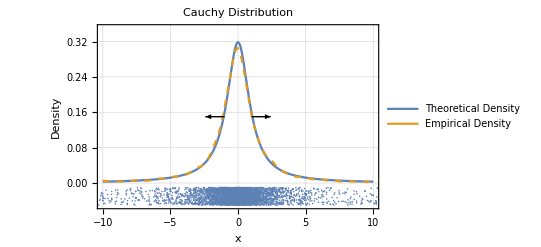

```mathematica
Show[
Plot[
{PDF[CauchyDistribution[0,1],x],
EmpiricalCauchyPDF
},
{x,-10,10},
PlotTheme->"Detailed",
PlotLegends->Placed[{
Style["Theoretical Density",Smaller],
Style["Empirical Density",Smaller]},
{{.77,.85},Center}],
PlotRange->{{-10,10},{-0.05,0.35}},
PlotLabel->"Cauchy Distribution",
FrameLabel->{"x","Density"},
(*Epilog->{Directive[Dashed,Gray],Line[{{1,-0.01},{1,0.35}}]},*)
Epilog->{
Arrowheads[Small],
Arrow[{{1,0.15},{1+√2,0.15}}],
Arrow[{{-1,0.15},{-1-√2,0.15}}]}
],
ListPlot[
Transpose@{CauchyVariates⟦1;;5000⟧,RandomReal[{-0.05,-0.01},5000]}(*,
Directive[LightBlue]*)
]
]
```

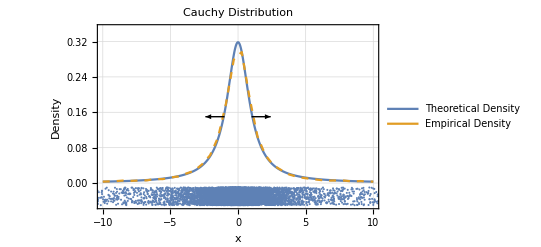
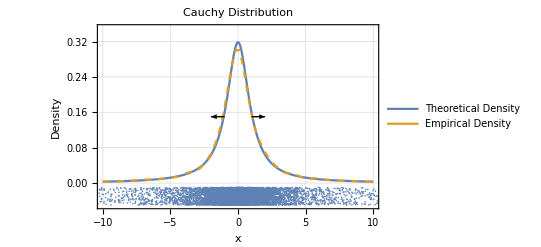
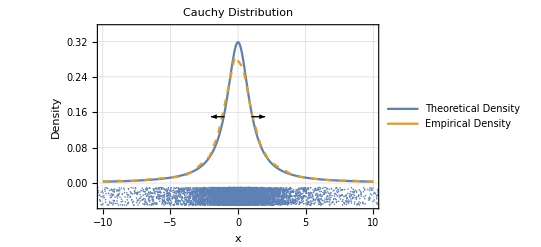
Saved Image
-Graphics-
-Graphics-
-Graphics-

Coupled Gaussian with κ = 0.5

```mathematica
KappaVariates=CoupledVariate[0,1,0.5,1000];
StudentTDistributionVariates=RandomVariate[StudentTDistribution[0,1,2],1000];
```

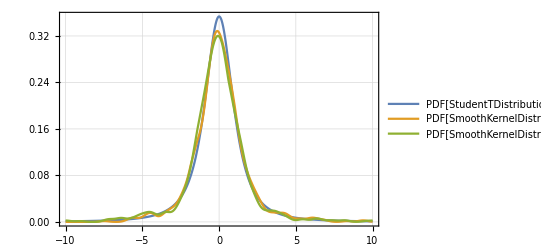

```mathematica
Plot[
{PDF[StudentTDistribution[2],x],
PDF[SmoothKernelDistribution[KappaVariates],x],
PDF[SmoothKernelDistribution[StudentTDistributionVariates],x]
},
{x,-10,10},
PlotTheme->"Detailed",
PlotRange->Full
]
(*Histogram[CauchyVariates,"Wand","PDF",
PlotRange->Full]*)
```

Coupled Gaussian with κ = 0.5

```mathematica
μ=1;σ=2;κ=0.5;
```

```mathematica
CoupledVariates=CoupledVariate[μ,σ,κ,10000];
```

```mathematica
EstimatedDensity=PDF[SmoothKernelDistribution[CoupledVariates,{"Adaptive",0.75,0.3}],x];
```

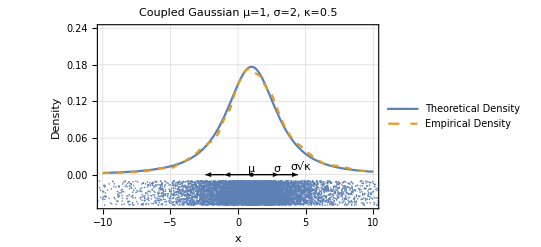

```mathematica
h=Graphics[Line[{{0,1/2},{0,-1/2}}]];
ArrowDetails={
Text["μ",{μ,f+0.01}],
Text["σ",{μ+σ-.1,f+0.01}],
Text["σ√κ",{μ+σ+σ √κ+.2,f+0.013}],
PointSize[Medium],
Point[{μ,f}],
Arrowheads[{{Medium,1,{h,0}}}],
Arrow[{{μ,f},{μ+σ,f}}],
Arrow[{{μ,f},{μ-σ,f}}],
Arrowheads[Medium],
Arrow[{{μ+σ,f},{μ+σ+σ √κ,f}}],
Arrow[{{μ-σ,f},{μ-σ-σ √κ,f}}]}/.
f->0;
Show[
Plot[
{PDF[CoupledNormalDistribution[μ,σ,κ],x],
Style[EstimatedDensity,Dashed]
},
{x,-10,10},
PlotTheme->"Detailed",
PlotRange->{{-10,10},{-0.05,0.24}},
PlotLegends->Placed[{
Style["Theoretical Density",Smaller],
Style["Empirical Density",Smaller]},
{{.27,.85},Center}],
PlotRange->Full,
PlotLabel->"Coupled Gaussian μ=1, σ=2, κ=0.5",
FrameLabel->{"x","Density"},
Epilog->ArrowDetails
],
ListPlot[
Transpose@{CoupledVariates,RandomReal[{-0.05,-0.01},10000]}(*,
Directive[LightBlue]*)
]
]
```

Coupled Gaussian with κ = -1/3

```mathematica
μ=1;σ=2;κ=-1/3;
CoupledVariates=CoupledVariate[μ,σ,κ,10000];
```

```mathematica
EstimatedDensity=PDF[SmoothKernelDistribution[CoupledVariates,{"Adaptive",0.75,0.5}],x];
```

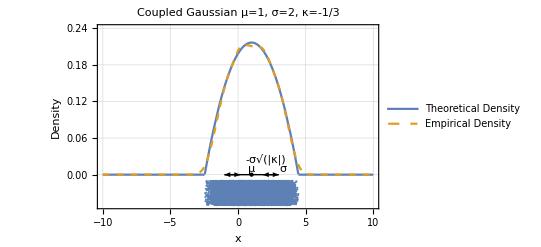

```mathematica
h=Graphics[Line[{{0,1/2},{0,-1/2}}]];
ArrowDetails={
Text["μ",{μ,f+0.01}],
Text["σ",{μ+σ+.3,f+0.01}],
Text["-σ√(|κ|)",{μ+σ+Sign[κ]σ √Abs[κ]+0.2,f+0.025}],
PointSize[Medium],
Point[{μ,f}],
Arrowheads[{{Medium,1,{h,0}}}],
Arrow[{{μ,f},{μ+σ,f}}],
Arrow[{{μ,f},{μ-σ,f}}],
Arrowheads[Medium],
Arrow[{{μ+σ,f},{μ+σ+Sign[κ]σ √Abs[κ],f}}],
Arrow[{{μ-σ,f},{μ-σ-Sign[κ]σ √Abs[κ],f}}]}/.
f->0(*PDF[CoupledNormalDistribution[μ,σ,κ],μ+σ]*);
Show[
Plot[
{PDF[CoupledNormalDistribution[μ,σ,κ],x],
Style[EstimatedDensity,Dashed]
},
{x,-10,10},
PlotTheme->"Detailed",
PlotRange->{{-10,10},{-0.05,0.24}},
PlotLegends->Placed[{
Style["Theoretical Density",Smaller],
Style["Empirical Density",Smaller]},
{{.27,.85},Center}],
PlotRange->Full,
PlotLabel->"Coupled Gaussian μ=1, σ=2, κ=-1/3",
FrameLabel->{"x","Density"},
Epilog->ArrowDetails
],
ListPlot[
Transpose@{CoupledVariates,RandomReal[{-0.05,-0.01},10000]}(*,
Directive[LightBlue]*)
]
]
```

### Higher values of coupling

Coupled Gaussian with κ = 2
	More samples (10,000) were needed for this validation
	And still does not seem to work

```mathematica
KappaVariates=CoupledVariate[0,1,2,10000];
StudentTDistributionVariates=RandomVariate[StudentTDistribution[0.5],10000];
```

```mathematica
EmpericalDensity=Style[PDF[SmoothKernelDistribution[
KappaVariates,
{"Adaptive",0.5,1}],
x],Dashed]
```

PDF[SmoothKernelDistribution[{1.11127,-0.752031,9996,-30.9036,-0.0196436},1],x]
 |  |  |  |

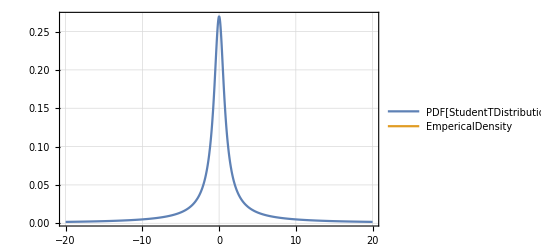

```mathematica
Plot[
{PDF[StudentTDistribution[0.5],x],
EmpericalDensity
},
{x,-20,20},
PlotTheme->"Detailed",
PlotRange->Full
]
```

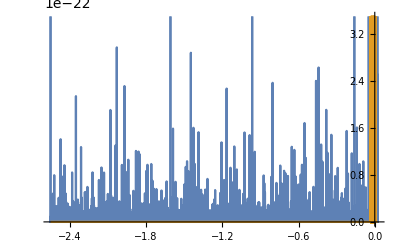

```mathematica
SmoothHistogram[{KappaVariates,StudentTDistributionVariates}]
```

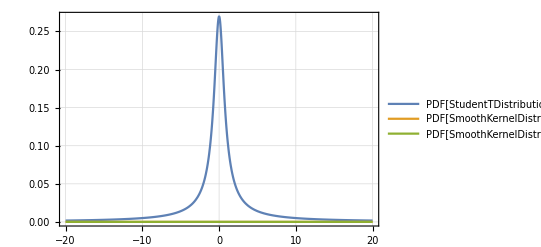

```mathematica
Plot[
{PDF[StudentTDistribution[0.5],x],
PDF[SmoothKernelDistribution[KappaVariates],x],
PDF[SmoothKernelDistribution[StudentTDistributionVariates],x]
},
{x,-20,20},
PlotTheme->"Detailed",
PlotRange->Full
]
(*Histogram[CauchyVariates,"Wand","PDF",
PlotRange->Full]*)
```

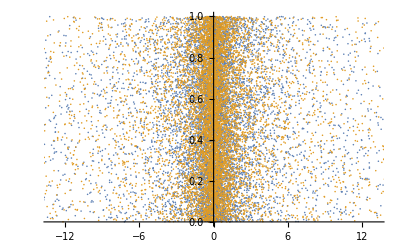

```mathematica
ListPlot[Map[Transpose,
{{KappaVariates,RandomReal[{0,1},10000]},
{StudentTDistributionVariates,RandomReal[{0,1},10000]}
}
]]
```

```mathematica
CoupledLogCounts[bins_,counts_]:=CoupledLogarithm[#,2,1]&/@(counts/Total[counts]);
```

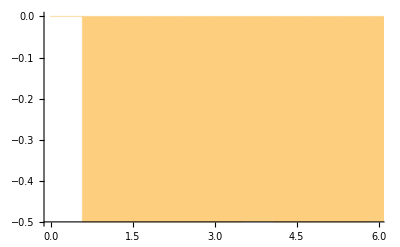
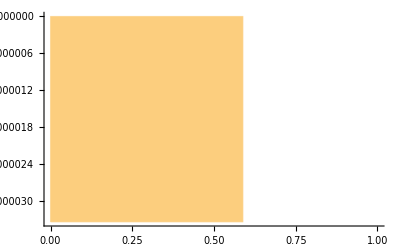

```mathematica
Histogram[#,
Automatic,CoupledLogCounts]&/@{KappaVariates^2,StudentTDistributionVariates^2}
```

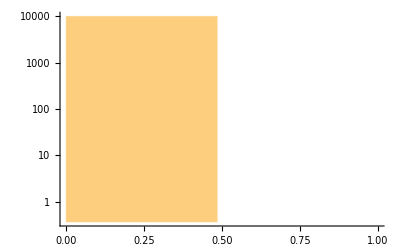
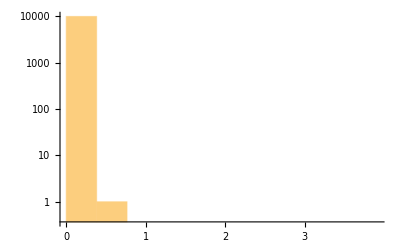

```mathematica
Histogram[#,
Automatic,{"Log","Count"}]&/@{KappaVariates^2,StudentTDistributionVariates^2}
```

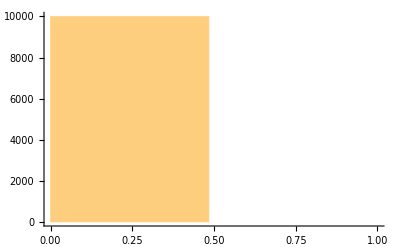
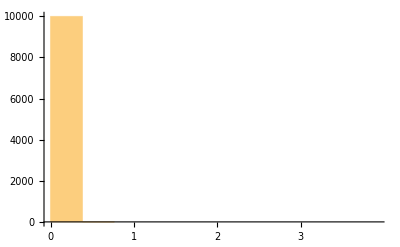

```mathematica
Histogram[#]&/@{KappaVariates^2,StudentTDistributionVariates^2}
```

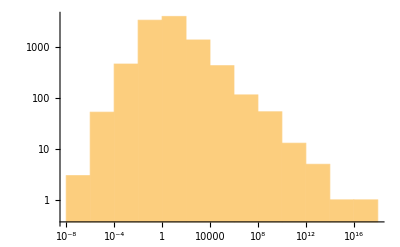
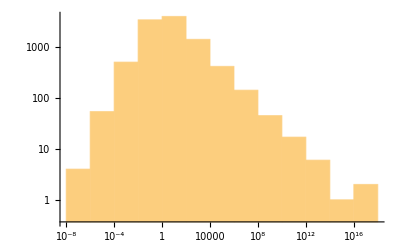

```mathematica
Histogram[#,
"Log",{"Log","Count"}]&/@{KappaVariates^2,StudentTDistributionVariates^2}
```

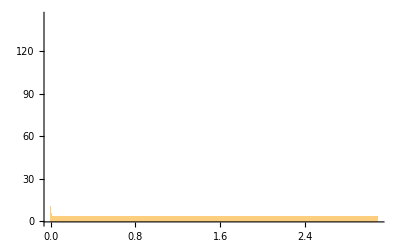
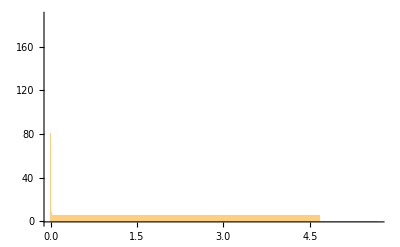

```mathematica
CoupledLogBins[bins_]:=CoupledLogarithm[#,2,1]&/@bins;
Histogram[#,
CoupledLogBins,CoupledLogCounts]&/@{KappaVariates^2,StudentTDistributionVariates^2}
```

```mathematica
&/@{"Sturges", "Scott","FreedmanDiaconis","Knuth","Wand"}
```

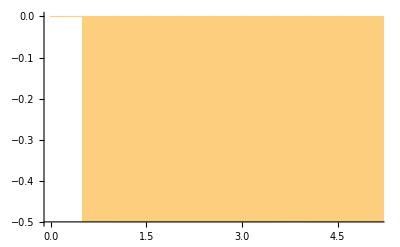

```mathematica
Histogram[KappaVariates^2,
"Knuth",CoupledLogCounts]
```

```mathematica
HistogramList[KappaVariates^2,
"Knuth",CoupledLogCounts]
```

{{0,5000000000000,10000000000000,15000000000000,20000000000000,25000000000000,30000000000000,35000000000000,40000000000000,45000000000000,50000000000000,55000000000000,11638,58250000000000000,58255000000000000,58260000000000000,58265000000000000,58270000000000000,58275000000000000,58280000000000000,58285000000000000,58290000000000000,58295000000000000,58300000000000000,58305000000000000},{1}}
 |  |  |  |

```mathematica
NormCounts[bins_,counts_]:=counts/Total[counts] [StudentTDistribution[0.5],0]
Histogram[1+2# PDF[StudentTDistribution[0.5],0]^2,
Log,CoupledLogCounts]&/@{KappaVariates^2,StudentTDistributionVariates^2}
```

{-Graphics-,-Graphics-}

### Understanding magnitude of fluctuations

Interested in understand the fluctuations of the scale of the coupled exponential distributions, particularly the coupled Gaussian distribution. From the generalized gamma distribution, a solution for the mean and standard deviation of the fluctuations can be derived but it has complex form.
-Graphics--Graphics-

```mathematica
FullSimplify[{Gamma[(-(1-1/κ))/2]/(√(2κ)Gamma[1/(2κ)]),1/(√(2κ))(Gamma[(-(2-1/κ))/2]/Gamma[1/(2κ)]-(Gamma[(-(2-1/κ))/2]/Gamma[1/(2κ)])^2)^(1/2)},κ∈Reals&&0<κ<∞]
```

{Gamma[1/2 (-1+1/κ)]/(√2 √κ Gamma[1/(2 κ)]),√((1-4 κ)/(1-2 κ)^2)}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

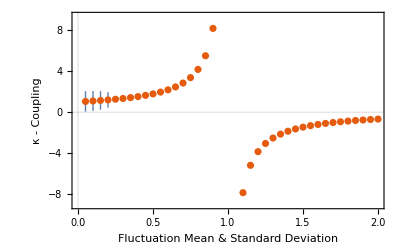

```mathematica
ListPlot[Table[{κ,Around[Gamma[(-(1-1/κ))/2]/(√(2κ)Gamma[1/(2κ)]),√((1-4 κ)/(1-2 κ)^2)]},
{κ,0,2,0.05}
],
PlotTheme->"Scientific",
FrameLabel->{"Fluctuation Mean & Standard Deviation","κ - Coupling"}
]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

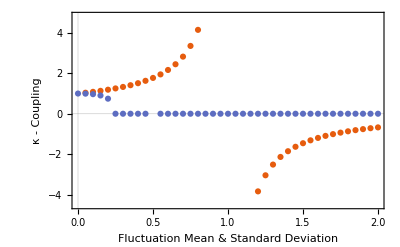

```mathematica
ListPlot[Table[{{κ,Re[Gamma[(-(1-1/κ))/2]/(√(2κ)Gamma[1/(2κ)])]},{κ,Re[√((1-4 κ)/(1-2 κ)^2)]}},
{κ,0,2,0.05}
]//Transpose,
PlotTheme->"Scientific",
FrameLabel->{"Fluctuation Mean & Standard Deviation","κ - Coupling"}
]
```